```mathematica
(*zad.1*)
FractionalPart[3+4i/5+2i]
3+4i/5+2i
IntegerPart[3+4i/5+2i]
FindRoot[4 x^2-3x-6==0,{x,1}]
```

FractionalPart[3+(14 i)/5]

3+(14 i)/5

IntegerPart[3+(14 i)/5]

{6.→1.65587}

```mathematica
(*zad.2*)
Integrate[(x^2-a^2)^3/2/x^3,x]
```

```mathematica
1/2 (a^6/(2 x^2)-(3 a^2 x^2)/2+x^4/4+3 a^4 Log[x])
Limit[(2n+1)/(3n+1),n->∞]
```

1/2 (a^6/(2 x^2)-(3 a^2 x^2)/2+x^4/4+3 a^4 Log[x])

2/3

```mathematica
D[1/5x^5*ArcTan[x]-1/20x^2+1/10x^2-1/10*Log10[1+x^2],x]
```

General::ivar: 6. is not a valid variable.

```mathematica
∂_6. 2187.706404143789
D[1/5 x^5*ArcTan[x]-1/20 x^2+1/10 x^2-1/10*Log10[1+x^2],x]
```

General::ivar: 6. is not a valid variable.

∂_6. 2187.71

General::ivar: 6. is not a valid variable.

∂_6. 2187.71

(-5. | -3.0802
-4. | -4.96944
-3. | 4.25452
-2. | 4.56473
-1. | -4.79462
0. | 0.
1. | -4.79462
2. | 4.56473
3. | 4.25452
4. | -4.96944
5. | -3.0802)

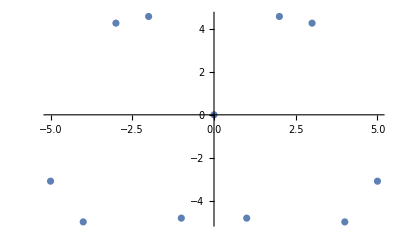

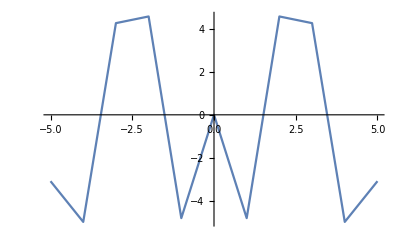

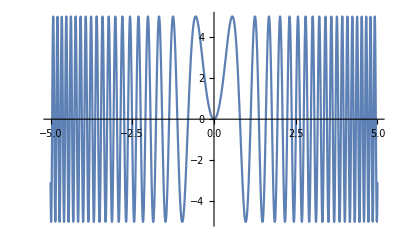

```mathematica
(*zad.3,4 *)
lw={};
For[x=-5.0,x≤5,x+=1,AppendTo[lw,{N[x],5Sin[5x^2]}]]
MatrixForm[lw]
ListPlot[lw]
ListLinePlot[lw]
Plot[{5Sin[5x^2]},{x,-5,5}]
```

```mathematica
(*zad.3 utworz liste wynikow ktoergo celem bedzie obliczenie w zakreesie -5>t>5 x=5sin(5t^2) zad4.Na podstawie listy wyników z zadania 3 narysuj nastepujace wykrsy linowy ounktowy oraz w staki logarytmicznej. Pamietaj o opisaniu osi calego wykresu*)
```

```mathematica
(*zad.5*)
Plot3D[{Sin[2x]*Cos[4y]},{x,-2Pi,2Pi},{y,-2Pi,2Pi},PlotStyle->{{Thickness[0.004],},{Thickness[0.004],Dashing[{0.02,0.015}],Black}},PlotLegends->{"sin[2x]*cos[4y]",Red},BaseStyle->{FontFamily->Times,FontSize->14},ImageSize->Scaled[0.7],PlotLabel->StyleForm["DWA WYKRESY RAZEM",FontSize->14,Green],Background->LightBlue,Ticks->{{-2Pi, 2Pi}, Automatic}]
```

-Graphics3D-